# List #3

## Exercise 1

We want to proof a theorem for a general 3x3 matrix:

```mathematica
ClearAll[A,a,b,c,d,e,f,g,h,i]
A={{a,b,c},{d,e,f},{g,h,i}}
FullSimplify[MatrixPower[A,3]-Tr[A]MatrixPower[A,2]+1/2((Tr[A])^2-Tr[MatrixPower[A,2]])A-Det[A]IdentityMatrix[3]]==0
```

{{a,b,c},{d,e,f},{g,h,i}}

{{0,0,0},{0,0,0},{0,0,0}}==0

## Exercise 2

We want to proof a theorem for two general 2x2 matrices:

```mathematica
ClearAll[A,B,a,b,c,d,e,f,g,h]
A={{a,b},{c,d}}
B={{e,f},{g,h}}
FullSimplify[(Tr[A.B]-Tr[A]Tr[B])IdentityMatrix[2]+Tr[B]A+Tr[A]B-A.B-B.A]//MatrixForm
```

{{a,b},{c,d}}

{{e,f},{g,h}}

(0 | 0
0 | 0)

## Exercise 3

We want to compute rankt of the matrices and find their biggest minor:

```mathematica
M1={{3,1,1,2,-1},{0,2,-1,1,2},{4,3,2,-1,1},{12,9,8,-7,3},{-12,-5,-8,5,1}}
MatrixRank[M1]
Minors[M1,MatrixRank[M1]]
```

{{3,1,1,2,-1},{0,2,-1,1,2},{4,3,2,-1,1},{12,9,8,-7,3},{-12,-5,-8,5,1}}

4

{{18,-8,16,14,0},{0,0,0,0,0},{54,-24,48,42,0},{36,-16,32,28,0},{0,0,0,0,0}}

```mathematica
M2={{1,1,1,1},{4,3,2,1},{1,4,1,1},{5,1,1,1},{1,1,3,1},{1,1,1,2}}
MatrixRank[M2]
Minors[M1,MatrixRank[M2]]
```

{{1,1,1,1},{4,3,2,1},{1,4,1,1},{5,1,1,1},{1,1,3,1},{1,1,1,2}}

4

{{18,-8,16,14,0},{0,0,0,0,0},{54,-24,48,42,0},{36,-16,32,28,0},{0,0,0,0,0}}

## Exercise 4

We present a table witch names of European Capital Cities and their temperature:

```mathematica
TmpCapt=CountryData["Europe","CapitalCity"];
TC=Table[TmpCapt[[i]][[2]][[1]],{i,1,Length[TmpCapt]}];
tc[u_]:=WeatherData[u,"Temperature"];
FinalCT=Map[tc,TC];
FinalData=Transpose[{TC,FinalCT}];
TableForm[FinalData,TableHeadings->{Table[" ",{k,1,Length[FinalData]}],{" "," "}}]
```

|   |  
  | Tirana | 12.
  | AndorraLaVella | 2.4
  | Vienna | 6.
  | Minsk | 1.
  | Brussels | 10.3
  | Sarajevo | 1.
  | Sofia | 10.
  | Zagreb | 9.3
  | Nicosia | 12.3
  | Prague | 9.5
  | Copenhagen | 7.
  | Tallinn | 3.
  | Torshavn | 4.8
  | Helsinki | 1.
  | Paris | 10.
  | Berlin | 10.7
  | Gibraltar | 13.
  | Athens | 10.8
  | SaintPeterPort | 12.
  | Budapest | 5.7
  | Reykjavik | -3.9
  | Dublin | 13.
  | Douglas | 12.
  | Rome | 5.
  | SaintHelier | 11.
  | Pristina | 6.2
  | Riga | 4.
  | Vaduz | 1.3
  | Vilnius | 2.
  | Luxemburg | 8.
  | Skopje | 3.6
  | Valletta | 16.8
  | Chisinau | 5.
  | MonacoVille | 8.8
  | Podgorica | 2.8
  | Amsterdam | 11.
  | Oslo | 0.
  | Warsaw | 4.
  | Lisbon | 12.6
  | Bucharest | 8.
  | SanMarino | 12.8
  | Belgrade | 8.
  | Bratislava | 5.6
  | Ljubljana | 4.9
  | Madrid | 5.
  | Longyearbyen | 1.
  | Stockholm | 0.
  | Bern | -0.8
  | Kiev | 2.
  | London | 13.
  | VaticanCity | 5.

## Exercise 5

We want to compute rankt of the matrix:

```mathematica
la={{7-λ,-12,6},{10,-λ-19,10},{12,-24,13-λ}}
Det[la]
MatrixRank[la]
```

{{7-λ,-12,6},{10,-19-λ,10},{12,-24,13-λ}}

-1+λ+λ^2-λ^3

3

## Exercise 6

We check Bernford Theorem with data of country population and temperature in capital cities:

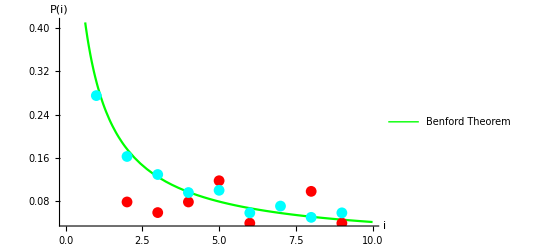

```mathematica
TDigits=Map[RealDigits,FinalCT[[All,1]]];
Dig=Table[TDigits[[i]][[1]][[1]],{i,1,Length[FinalCT]}];
EqN[n_,x_]:=If[n==x,1,0]
Tempd=Table[0,{i,1,9}];
For[k=1,k≤9,k++,For[i=1,i≤Length[Dig],i++,If[Dig[[i]]==k,Tempd[[k]]++,]]];
Tempd=Tempd/Length[Dig]//N;
Temp=ListPlot[Tempd,PlotStyle->Red];

Nms=Table[CountryData[All][[i]][[2]],{i,1,Length[CountryData[All]]}];
GivePop[name_]:=CountryData[name,"Population"]
Pops=Map[GivePop,Nms][[All,1]];
PopDigits=Map[IntegerDigits,Pops][[All]];
DigP=Table[PopDigits[[i]][[1]],{i,1,Length[Pops]}];
Popd=Table[0,{i,1,9}];
For[k=1,k≤9,k++,For[i=1,i≤Length[DigP],i++,If[DigP[[i]]==k,Popd[[k]]++,]]];
Popd=Popd/Length[Pops]//N;
PopPlot=ListPlot[Popd,PlotStyle->Cyan];

Theorem=Plot[Log10[1+1/x],{x,0,10},PlotStyle->Green,AxesLabel->{"i","P(i)"},PlotLegends->{LineLegend[{Green},{"Benford Theorem"}],PointLegend[{Red,Cyan},{"Temperatures","Population"}]}];
Show[Theorem,Temp,PopPlot]
```

## Exercise 7

We define function which returns list of countries which first letter of name starst with on of the two letters provided as arguments:

```mathematica
Chars=Map[Characters,Nms];
LetList[fl_,sl_]:=Module[{},
AG=List[];
For[i=1,i<=Length[Nms],i++,If[Characters[Nms[[i]]][[1]]==fl || Characters[Nms[[i]]][[1]]==sl,AG=Flatten[{AG,Nms[[i]]}],]];
Return[AG]]
out=LetList["A","G"]//TableForm
```

Afghanistan
Albania
Algeria
AmericanSamoa
Andorra
Angola
Anguilla
AntiguaBarbuda
Argentina
Armenia
Aruba
Australia
Austria
Azerbaijan
Gabon
Gambia
GazaStrip
Georgia
Germany
Ghana
Gibraltar
Greece
Greenland
Grenada
Guadeloupe
Guam
Guatemala
Guernsey
Guinea
GuineaBissau
Guyana

## Exercise 8

We want to show temperatures in Capital cities of Poland’s Neighbours:

```mathematica
Neighbors=Table[CountryData["Poland","BorderingCountries"][[i]][[2]],{i,1,Length[CountryData["Poland","BorderingCountries"]]}];
NeighborsCapitols=Table[CountryData[Neighbors[[i]],"CapitalCity"][[2]][[1]],{i,1,Length[CountryData["Poland","BorderingCountries"]]}];
NTemps=Map[tc,NeighborsCapitols];
```

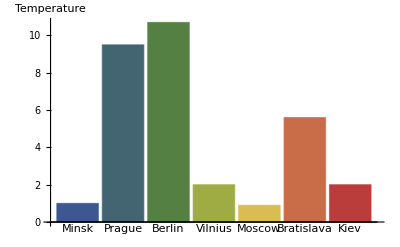

```mathematica
BarChart[NTemps,ChartLabels->NeighborsCapitols,AxesLabel->{None,"Temperature"},ChartStyle->"DarkRainbow"]
```

## Exercise 9